# Results after relaxation

Before introducing thermal dynamics, we need to create a stable skyrmion by evaluating the LLG equation at zero temperature, called the relaxation stage. Once a stable skyrmion is found for a set of material parameters, we can turn on temperature and evaluate the stochastic LLG equation using pulse-noise dynamics. This notebook is used to confirm that before dynamics, skyrmion relaxation ran correctly. 

We show:
 - Matrix plot of spin field after relaxation
 - ListPlot of topological charge during relaxation 
 - ListPlot of energy during relaxation
 - ListPlot of topological charge during relaxation

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
plotSize = 1000; (* Set size of plots generated *)

(* Set options for plot formatting *)
SetOptions[{MatrixPlot,ListVectorPlot},ImageSize->plotSize,ImagePadding->{{50,70},{50,50}},LabelStyle->{Directive["Times",14,Black],FontFamily->"Times"}];
SetOptions[{ListPlot,ListLogPlot,ListLogLogPlot,Plot,LogPlot,LogLogPlot,Histogram},Frame->True,AspectRatio->1/GoldenRatio,ImageSize->plotSize,LabelStyle->{Directive["Times",18,Black],FontFamily->"Times",ImagePadding->{{100,100},{100,100}}}];
```

## Functions

```mathematica
(* 

This function imports data from Directory[]<>"/data/thermal-collapse-data". It takes in a string, "type", that refers to a particular set of data and imports the appropriate file.;
Input: type = string, must be one of {"spin","energy","topcharge","effsize"}, T = temperature, H = external field, A = DMI constant, ED = Dipole-Dipole constant, PMA = perpendicular magnetic anisotropy constant (Last 5 inputs can be either floats or strings);
Output: Array of data. Structure depends on type of data imported
*)
getRelaxationData[type_,T_,H_,A_,ED_,PMA_]:=Block[{relDir,fileSuffix,data},

relDir="data/raw-collapse-data-skyrmion/";
fileSuffix ="_T="<>ToString[T]<>"_H="<>ToString[H]<>"_DMI="<>ToString[A]<>"_DDI="<>ToString[ED]<>"_PMA="<>ToString[PMA]<>"_*.h5";

Which[
type=="spin",
data=ToExpression[Import[relDir<>"spin_field_after_relaxation"<>fileSuffix,"Data"]],

type=="energy",
data=ToExpression[Import[relDir<>"energy_during_relaxation"<>fileSuffix,"Data"]],

type=="topcharge",
data=ToExpression[Import[relDir<>"topological_charge_during_relaxation"<>fileSuffix,"Data"]],

type=="effsize",
data=ToExpression[Import[relDir<>"effective_size_during_relaxation"<>fileSuffix,"Data"]]

];
data[[1,1]]
]
```

## Plot relaxation results

```mathematica
Tchoice="0.0"; (* For relaxation, this parameter must be set to zero *)
Hchoice=-0.0014;
Achoice=0.02;
EDchoice="0.0";
PMAchoice="0.0";

(* NOTE: Any parameter set to zero must be input as the string "0.0". Inputing as a float or int will cause mathematica to define the filename incorrectly *)
```

Spin field

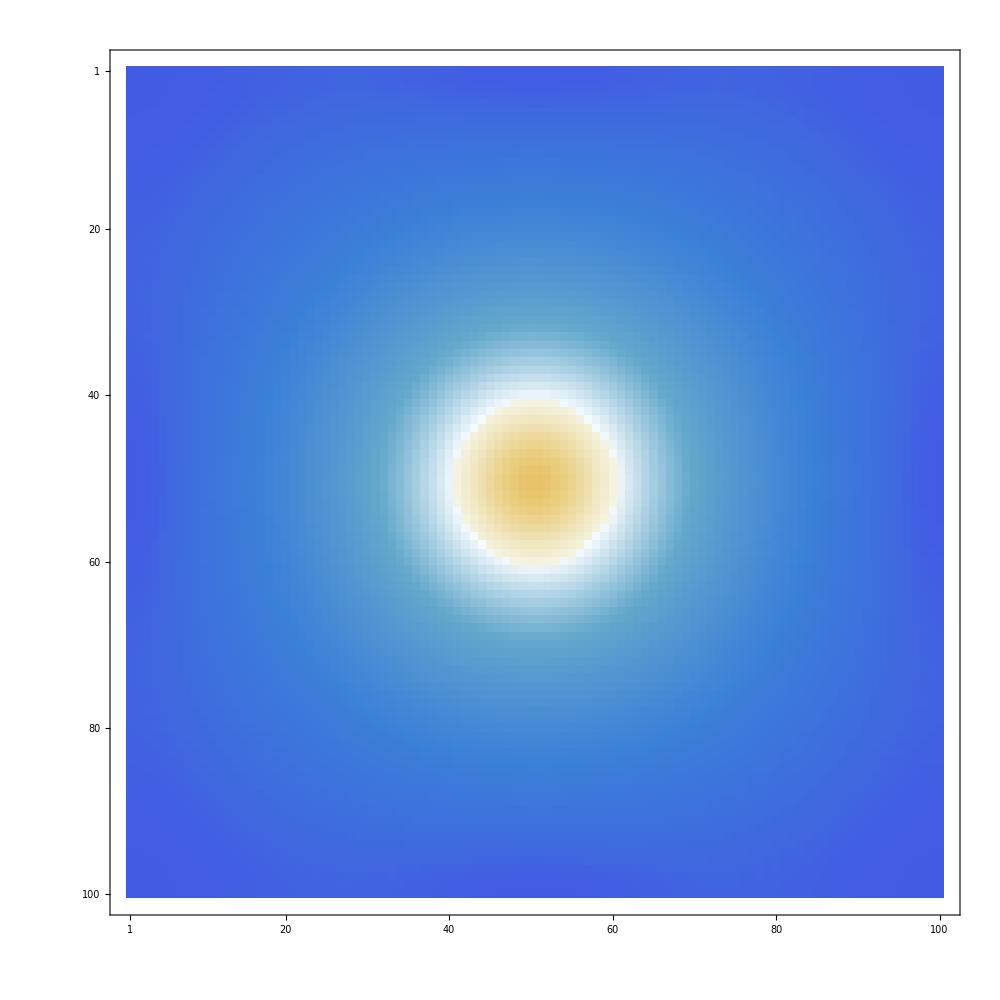

```mathematica
spindata=getRelaxationData["spin",Tchoice,Hchoice,Achoice,EDchoice,PMAchoice];
MatrixPlot[spindata[[All,All,3]]]
```

Energy during relaxation

```mathematica
endata=getRelaxationData["energy",Tchoice,Hchoice,Achoice,EDchoice,PMAchoice];
ListPlot[endata,PlotRange->All]
```

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

ListPlot::lpn: $Failed⟦1,1⟧ is not a list of numbers or pairs of numbers.

ListPlot[$Failed⟦1,1⟧,PlotRange→All]

Effective size during relaxation

```mathematica
esdata=getRelaxationData["size",Tchoice,Hchoice,Achoice,EDchoice,PMAchoice];
ListPlot[esdata,PlotRange->All]
```

Part::partd: Part specification data⟦1,1⟧ is longer than depth of object.

ListPlot::lpn: data⟦1,1⟧ is not a list of numbers or pairs of numbers.

ListPlot[data⟦1,1⟧,PlotRange→All]

Topological charge during relaxation

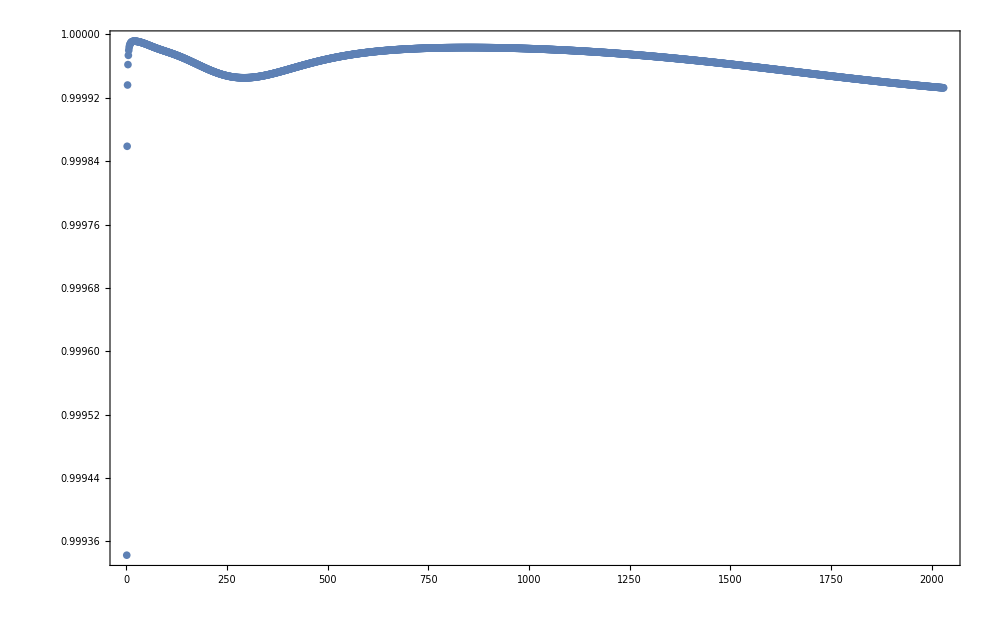

```mathematica
tcdata=getRelaxationData["topcharge",Tchoice,Hchoice,Achoice,EDchoice,PMAchoice];
ListPlot[tcdata,PlotRange->All]
```